```mathematica
Clear[src,outp];
src=NotebookDirectory[];
outp=src~~"output\\";
CloudGet[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/myPackageWL.wl"]];

evalfiles = Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/url-evaluation-files.m"];
```

```mathematica
transl=.
transl={"variable","date","time","name","atmospheric pressure","temperature","humidity","height above German reference surface","tidal volume","breathing frequency","expiratory reserve volume","inspiratory vital capacity","expiratory vital capacity","forced expiratory volume 1 sec","forced vital capacity","peak expiratory flow","maximal (mid-)expiratory flow 25%","maximal (mid-)expiratory flow 50%","maximal (mid-)expiratory flow 75%","residual volume","total lung capacity","alveolar volume","functional residual capacity","haemoglobin","inspiratory concentration helium","expiratory concentration helium","inspiratory concentration carbon monoxide","expiratory concentration carbon monoxide","diffusion capacitance carbon monoxide"};

exportlist=.
exportlist={{"ID","age","height","sex","dlco","tlco","kcosi","kcotr","inspiratory_concentration_helium","expiratory_concentration_helium","inspiratory_concentration_carbon_monoxide","expiratory_concentration_carbon_monoxide","va","ethnic","fev1","fvc","maximal_(mid-)expiratory_flow_25%","fef2575","fef75","fev075","peak_expiratory_flow","frc","tlc","rv","erv","ic","expiratory_vital_capacity","vc","tidal_volume","breathing_rate_1/min","atmospheric_pressure","temperature","humidity","height_above_German_reference_surface"}};

Map[
(respData=.;
respData=StringSplit[Import[#[[3]]],"\n"];
respData=StringSplit[Flatten@respData[[15;;Length@respData]],"  "]/.""->Nothing;
respData[[All,1]]=StringReplace[#,{DigitCharacter->"",".94"->"oe"}]&/@respData[[All,1]];
respData[[1]]=Prepend[respData[[1]],"Variable"];
respData=StringReplace[#," "->""]&/@respData;
respData[[All,1]]=transl;
(*TableForm[respData]*)

varProb=.;
varProb=Import[#[[2]]];
varProb=Flatten[StringCases[varProb,#]&/@{"Geschlecht--" ~~Shortest[a__]~~","->a,"Geburtsjahr--" ~~Shortest[a__]~~","->a,"Groesse--" ~~Shortest[a__]~~","->a}];
varProb=varProb/.{"maennlich"->"M","weiblich"->"F","divers"->"M"};
varProb[[2]]=2023-ToExpression[varProb[[2]]];
varProb;

AppendTo[exportlist,varProb[[{2,3,1}]]];
(*
TableForm[Transpose[Prepend[{respData},Table[i,{i,Length@respData}]]]]
*)

PrependTo[exportlist[[-1]],StringCases[respData[[4,2]],DigitCharacter..][[1]]]; (*ID*)


AppendTo[exportlist[[-1]],{"",respData[[-1,4]],"","",respData[[25,4]],respData[[26,4]],respData[[27,4]],respData[[28,4]],respData[[22,4]],0,respData[[14,4]],respData[[15,4]],respData[[17,4]],respData[[18,4]],respData[[19,4]],"",respData[[16,4]],respData[[23,4]],respData[[21,4]],respData[[20,4]],respData[[11,4]],respData[[12,4]],respData[[13,4]],"",Min[ToExpression/@respData[[9,-3;;-1]]] (*Slow Vital Capacity != tidal volume*),Min[ToExpression/@respData[[10,-3;;-1]]] ,StringCases[respData[[5,2]],DigitCharacter..][[1]],
StringCases[respData[[6,2]],DigitCharacter..][[1]],
StringCases[respData[[7,2]],DigitCharacter..][[1]],
StringCases[respData[[8,2]],DigitCharacter..][[1]]
}];
exportlist=Map[Flatten[#]&,exportlist,{1}];

)&,evalfiles];
Export[outp~~"lung function testing.xlsx",exportlist]
```

C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\output\lung function testing.xlsx

## Upload on http://gli-calculator.ersnet.org/index.html for explanation see http://gli-calculator.ersnet.org/docs.html

```mathematica
replList=.
fn=.
fn=Import["H:\\Projekte\\Quantifizierung humane Aerosolemission\\Datenerhebung und Auswertung\\full names GLI variables.xlsx"];
replList=(#[[1]]->#[[2]])&/@Partition[Flatten@fn,2];

(*
idList=.
idList=StringReplace[Flatten[StringCases[evalfiles[[All,3]],"\\"~~NumberString ..~~"\\"]],"\\"->""];
PrependTo[idList,"ID"];
*)

respData=.
respData=Import["H:\\Projekte\\Quantifizierung humane Aerosolemission\\Datenerhebung und Auswertung\\lung function testing_GLI.xlsx"][[1]];

(*
respData=Map[Flatten[#]&,Transpose[{idList,respData}],{1}];
*)


z=0;
delList=.
delList=Map[(z=z+1;If[Union[#[[2;;-1]]]=={0},z,Nothing])&,Transpose@respData];
 (*lösche Spalten mit 0*)

respData=Transpose@Delete[Transpose@respData,{#}&/@delList];
respData[[1]]=respData[[1]]/.replList;


cvTOvcMale=.
cvTOvcMale[age_Real]:=Module[{},{0.562+0.357 *age,"±2 SEE:",4.15}] (*Closing Volume as % of vital capacity  with 2 Standrad Deviations*)
cvTOvcFemale=.
cvTOvcFemale[age_Real]:=Module[{},{2.812+0.293 *age,"±2 SEE:",4.90}]
(* the closing volume is the endexpiratory volume before total expiration. the here calculated volume is the volume, where no bronchiole closing occurs (the non-closing-volume)  *)
closingVolume=.
closingVolume[l_List]:=Module[{f},If[l[[4]]=="M",f=cvTOvcMale,f=cvTOvcFemale];{f[l[[2]]],{(1-(f[l[[2]]][[1]]/100))*l[[22]],f[l[[2]]][[-1]]*l[[22]]/100}}]

cvList=Transpose[closingVolume/@Rest@respData];
PrependTo[cvList[[1]],"closing volume as percent of vital capacity with 2 Std Dev [from Buis & Ross: Predicted Values for Closing Volumes(...). Amer Rev of Resp Dis 1973]"];
PrependTo[cvList[[2]],"vital capacity - closing volume with 2 Std Dev [from Buis & Ross: Predicted Values for Closing Volumes(...). Amer Rev of Resp Dis 1973]"];

respData=Join[Transpose@respData,cvList];

respDataXLSX=respData;
respDataXLSX[[-2]][[2;;-1]]=StringJoin[ToString@#[[1]]~~" ± "~~ToString@#[[-1]]]&/@Rest@respDataXLSX[[-2]];
respDataXLSX[[-1]][[2;;-1]]=StringJoin[ToString@#[[1]]~~" ± "~~ToString@#[[-1]]]&/@Rest@respDataXLSX[[-1]];

Export[outp~~"lung function testing with GLI references.xlsx",Transpose@respDataXLSX]

Export[outp~~"lung function testing with GLI references.m",Transpose@respData]
```

H:\Projekte\Quantifizierung humane Aerosolemission\Datenerhebung und Auswertung\lung function testing with GLI references.xlsx

H:\Projekte\Quantifizierung humane Aerosolemission\Datenerhebung und Auswertung\lung function testing with GLI references.m

```mathematica
test=.
test=Rest[Select[Transpose[respData],StringContainsQ[#[[1]],"Alveolar Volume Percent Predicted"]&][[1]]];
FindDistribution@test
CDF[FindDistribution@test]
```

$Aborted

Function[x,1/2 Erfc[0.059941 (92.2602-x)]]

```mathematica
data=.
data=Select[Transpose[respData],StringContainsQ[#[[1]],"Percent Predicted"]&]
```

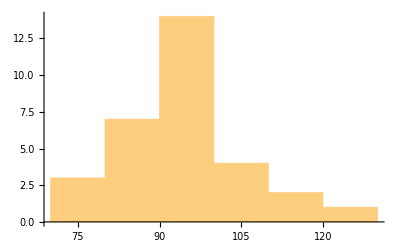
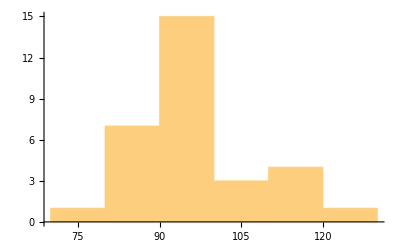
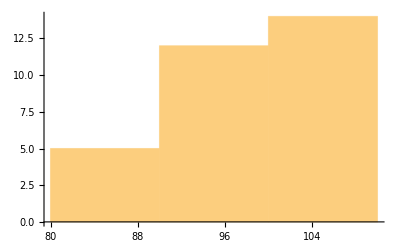
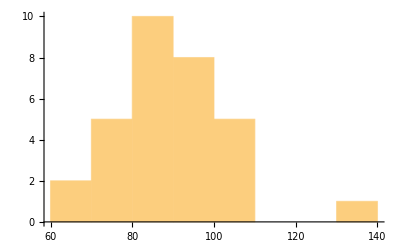
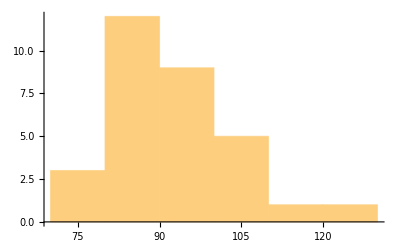
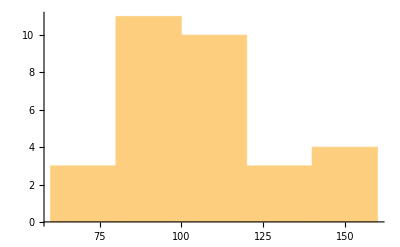
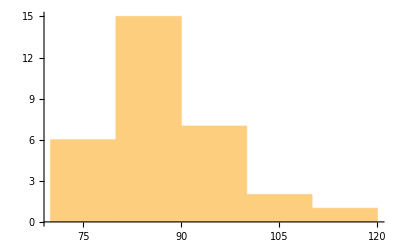
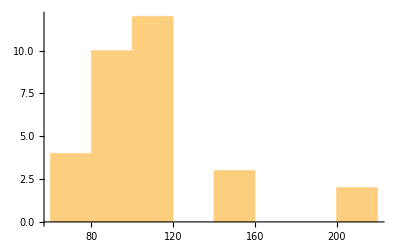
-Graphics- | FEV1 Percent Predicted
-Graphics- | FVC Percent Predicted
-Graphics- | FEV1/FVC Percent Predicted
-Graphics- | TLCO Percent Predicted
-Graphics- | Alveolar Volume Percent Predicted
-Graphics- | FRC Percent Predicted
-Graphics- | TLC Percent Predicted
-Graphics- | RV Percent Predicted
-Graphics- | RVTLC Percent Predicted
-Graphics- | ERV Percent Predicted
-Graphics- | IC Percent Predicted

```mathematica
TableForm@Transpose@{Histogram/@Rest/@data,data[[All,1]]}
```

```mathematica
respData
```